```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v3";
SetDirectory[workingdirectory];
matrixfilenames=Select[FileNames[All,"./results"],StringMatchQ[#,"*mat_npp0.5^+*"]&]
dim=Range[Length[matrixfilenames]];
```

{./results/mat_npp0.5^+}

```mathematica
normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)])}]
decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[{(Transpose[Oμ].ham).Oμ,(Transpose[Oμ].norm).Oμ}];];
```

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
HNc={};HNuc={};
thr=10^-23;

Do[
str=OpenRead[matrixfilenames[[i]],BinaryFormat->True];
headmarker=BinaryRead[str,"Integer32",ByteOrdering->$ByteOrdering];
NormHamMat=BinaryReadList[str,"Real64",ByteOrdering->$ByteOrdering];
JbasisDim=IntegerPart[Sqrt[Length[NormHamMat]*0.5]];
Close[str];

norm=ArrayReshape[NormHamMat[[1;;JbasisDim^2]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+1;;]],{JbasisDim,JbasisDim}];
decompose[thr,norm,ham];

evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
  renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

evn=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];

Print["Condition number ℕ_ij = ",Max[Abs[evn]]/Min[Abs[evn]]];
Print["EV_full(ℍ) = ",evhamnorm[[-2;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[-2;;]]];

thh=100;(*Max[Abs[λs]];*)
AppendTo[HNc,evn];
AppendTo[HNuc,evhamunnorm];
,{i,dim}]

(*Grid[{{"ev(⟨i|j⟩)\n","ev(⟨i|H_nucl|j⟩)","ev(⟨α|H_nucl|β⟩) ev(𝟙) > "ScientificForm[thr]},{Sort[evn,Re[#1]>Re[#2]&]//MatrixForm,Sort[Eigenvalues[{ham,norm}],R~e[#1]>Re[#2]&]//MatrixForm,Sort[λs,Re[#1]>Re[#2]&]//MatrixForm}}]*)
```

Condition number ℕ_ij = 19225.1

EV_full(ℍ) = {15.2709,3.71544}

EV_(EV (𝟙) > threshold)(ℍ) = {15.2709,3.71544}

```mathematica
HNc
```

{{2.09472,2.0122,1.98735,1.90504,1.00621,1.00081,1.00081,0.999186,0.999186,0.993789,0.000227568,0.000217926,0.000138076,0.000108957}}

```mathematica
data1={};
data2={};
Do[
AppendTo[data1,Select[Re[HNuc[[i]]],Abs[#]<thh&]];AppendTo[data2,Select[Re[HNc[[i]]],Abs[#]<thh&]];
,{i,dim}]
```

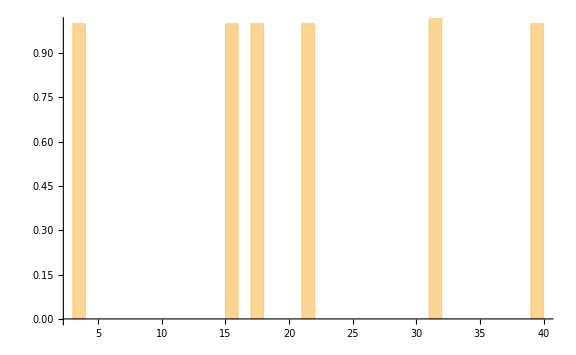

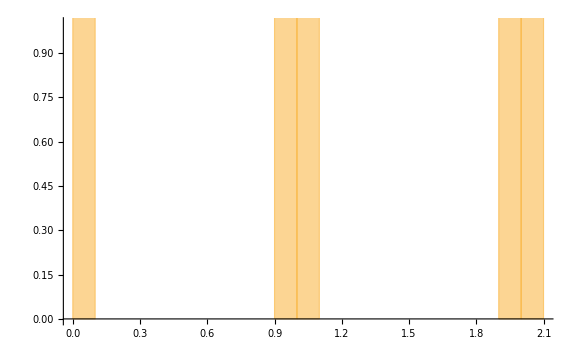

```mathematica
Histogram[data1,{1},PlotRange->{Automatic,{0,1}},ImageSize->Large]
Histogram[data2,{.1},PlotRange->{Automatic,{0,1}},ImageSize->Large]
```

```mathematica
norm//MatrixForm
```

(1. | 0.0474123 | -0.999876 | -0.0486313 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0474123 | 1. | -0.0462224 | -0.999876 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.999876 | -0.0462224 | 1. | 0.0474124 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0486313 | -0.999876 | 0.0474124 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.00621092 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.00621092 | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.00621094 | 0.999777 | 0.0064651 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.00621094 | 1. | 0.00596647 | 0.999777 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.999777 | 0.00596647 | 1. | 0.00621099 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0064651 | 0.999777 | 0.00621099 | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.000813658 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000813658 | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.000813679
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000813679 | 1.)

```mathematica
Chop[ham]//MatrixForm
```

(1363.99 | 17.7659 | -1379.82 | -18.2633 | -0.57523 | -0.00141056 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.7659 | 4.80369 | -17.8613 | -4.85743 | -0.0357853 | -0.10775 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1379.82 | -17.8613 | 1396.04 | 18.3608 | 0.573215 | 0.00136487 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-18.2633 | -4.85743 | 18.3608 | 4.91497 | 0.0366982 | 0.107373 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.57523 | -0.0357853 | 0.573215 | 0.0366982 | 1497.28 | 2.58042 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00141056 | -0.10775 | 0.00136487 | 0.107373 | 2.58042 | 21.8697 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1268.79 | 1.74313 | 1281.63 | 1.82051 | 0.304322 | 0.000100391 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.74313 | 24.1552 | 1.71298 | 24.3611 | 0.00241601 | 0.0570047 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1281.63 | 1.71298 | 1295.14 | 1.78899 | 0.304452 | 0.0000964286 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.82051 | 24.3611 | 1.78899 | 24.5818 | 0.00251511 | 0.0570291 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.304322 | 0.00241601 | 0.304452 | 0.00251511 | 1180.03 | 0.110547 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.000100391 | 0.0570047 | 0.0000964286 | 0.0570291 | 0.110547 | 31.8983 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1171.21 | 0.100524
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.100524 | 31.982)